[03-02-2025]
Calculus in  mathematica

Analytical integration

```mathematica
Integrate[Log[x]/x,x]
```

Log[x]^2/2

```mathematica
Integrate[Log[x]/x,{x,1,2}] (*Definite integration*)
```

Log[2]^2/2

```mathematica
Integrate[Log[x y]/x,x]
```

1/2 Log[x y]^2

```mathematica
Integrate[Log[x y]/(x y),x,y](*integrates over the geometric region*)
```

1/6 Log[x y]^3

```mathematica
Integrate[Log[x y]/x,{x,1,2},{y,1,2}] (*Definite integration with a numerical value*)
```

1/2 Log[2] (-2+Log[32])

Numerical integration

```mathematica
NIntegrate[1/(√(1+t+t^2)),{t,0,2}] (*Alternatively, one may use //N after integrate*)
```

1.23271

```mathematica
(*Now we want some coefficient...*)

(*NIntegrate[1/(√(1+a t+t^2)),{t,0,2}] , but 'a' must be defined through a function.
The delayed command {:=} defines the function, without attempting to evaluate it.*)
f[a_]:=NIntegrate[1/(√(1+a t+t^2)),{t,0,2}]
f[2]
```

1.09861

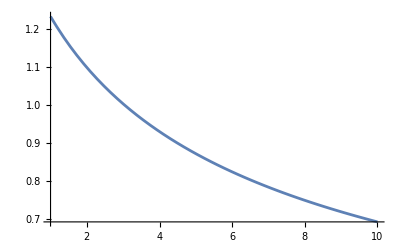

```mathematica
Plot[f[a],{a,1,10}]
```

HA: Take a function which isn’t analytically solvable, and evaluate it numerically.

```mathematica
Integrate[Exp[-x^2/2]/(2 Pi),x](*Can't be evaluated analytically!*)
(*NIntegrate needs a range for independent variable*)
NIntegrate[Exp[-x^2/2]/(2 Pi),{x,-10,10}]
```

Erf[x/(√2)]/(2 √(2 π))

0.398942

Solving differential equations

```mathematica
DSolve[z'[t]==-2 z[t],z[t],t]
```

{{z[t]→ⅇ^(-2 t) C[1]}}

```mathematica
DSolve[{x1'[t]==-2 x1[t],x1[0]==1},x1[t],t](*x^•[t] won't help!*)
```

{{x1[t]→ⅇ^(-2 t)}}

Coupled DE

```mathematica
DSolve[{x2'[t]==-y2[t],y2'[t]==-x2[t]},{x2[t],y2[t]},t]
```

{{x2[t]→1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2],y2[t]→-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]}}

```mathematica
(*The auxilary conditions need to be defined for determining the constants*)
dsol=DSolve[{x2'[t]==-y2[t],y2'[t]==-x2[t],x2[0]==2,y2[0]==1},{x2[t],y2[t]},t]
```

{{x2[t]→1/2 ⅇ^-t (3+ⅇ^(2 t)),y2[t]→-1/2 ⅇ^-t (-3+ⅇ^(2 t))}}

```mathematica
(*Plot[DSolve[{x'[t]==-y[t],y'[t]==-x[t],x[0]==2,y[0]==1},{x[t],y[t]},t],{t,0,10}]  Bad approach,extract the solutions first*)
dsol[[1]]
```

{x2[t]→1/2 ⅇ^-t (3+ⅇ^(2 t)),y2[t]→-1/2 ⅇ^-t (-3+ⅇ^(2 t))}

```mathematica
(*Extracting x and y separately*)
X[t_]=x2[t]/.dsol[[1]]
```

1/2 ⅇ^-t (3+ⅇ^(2 t))

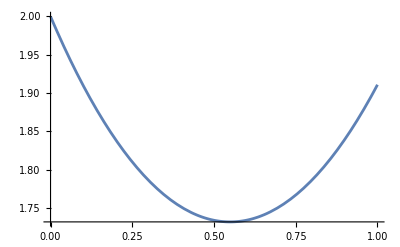

```mathematica
Plot[X[t],{t,0,1}]
```

```mathematica
Y[t_]=y2[t]/.dsol[[1]]
```

-1/2 ⅇ^-t (-3+ⅇ^(2 t))

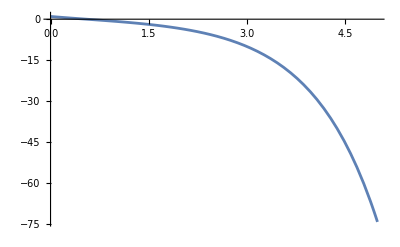

```mathematica
(*Wrong Wrong Wrong! Plot[Y[t_],{t,0,5}]*)
Plot[Y[t],{t,0,5}]
```

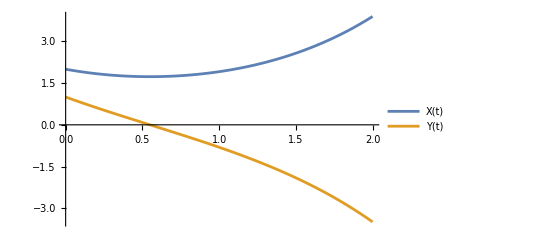

```mathematica
Plot[{X[t],Y[t]},{t,0,2},PlotLegends->"Expressions"]
```

Damped harmonic oscillator

```mathematica
DSolve[x4''[t]==-x4[t],x4[t],t]
```

{{x4[t]→C[1] Cos[t]+C[2] Sin[t]}}

```mathematica
DSolve[x5''[t]==-x5[t]-x5'[t],x5[t],t]
```

{{x5[t]→ⅇ^(-t/2) C[2] Cos[(√3 t)/2]+ⅇ^(-t/2) C[1] Sin[(√3 t)/2]}}

> Plotting without initial conditions (Analytical solving)

```mathematica
dsol1=DSolve[{x6''[t]==-x6[t]-x6'[t],x6[0]==1,x6'[0]==0},x6[t],t]
```

{{x6[t]→1/3 ⅇ^(-t/2) (3 Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])}}

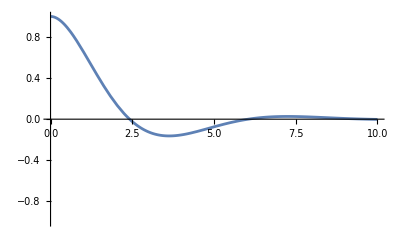

```mathematica
X1[t_]=x6[t]/.dsol1[[1]];
Plot[X1[t],{t,0,10},PlotRange->{-1,1}]
```

> Plotting with initial conditions (Numerical solving)

```mathematica
dsol2=NDSolve[{x7''[t]==-x7[t]-x7'[t],x7[0]==1,x7'[0]==0},x7[t],{t,0,10}]
```

{{x7[t]→InterpolatingFunction[…][t]}}

```mathematica
X2[t_]=x7[t]/.dsol2[[1]];
Plot[X2[t],{t,0,10},PlotRange->{-1,1}](*Which is the same as above*)
```

-Graphics-

```mathematica
dsol3= NDSolve[{x8''[t]==-x8[t]-0.5  x8'[t] ,x8[0]==1,x8'[0]==0},x8[t],{t,0,10}]
```

{{x8[t]→InterpolatingFunction[…][t]}}

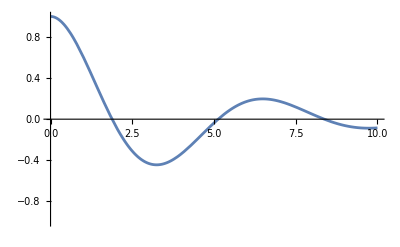

```mathematica
Plot[X3[t]=x8[t]/.dsol3[[1]],{t,0,10},PlotRange->{-1,1}](* writing X3[t_] would also give the same output*)
```

But, analytical solving doesn’t always help, for instance -

Example of a non linear DE

```mathematica
(*DSolve[x''[t]==-x[t]-0.5 x'[t] x[t]^2,x[t],t] throws error*)
```

```mathematica
dsol4 = NDSolve[{x9''[t]==-x9[t]- 0.5 x9'[t] x9[t]^2,x9[0]==1,x9'[0]==0},x9[t],{t,0,10}]
```

{{x9[t]→InterpolatingFunction[…][t]}}

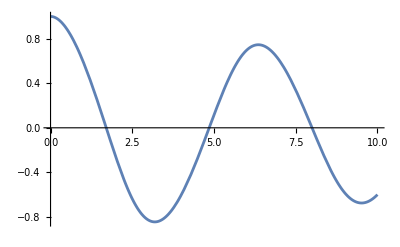

```mathematica
Plot[X9[t]=x9[t]/.dsol4[[1]],{t,0,10}]
```

```mathematica
ClearAll["`*"](*Clear all symbols in the current context*)
```

[04-02-2025]
Damped LCR circuit -  initial value problem

L di/dt=-Q/C- Ri
→     (d^2 Q)/dt^2=-Q/LC- R/L dQ/dt
 
Relevant time scales (as there’s no length here) of this system
1) Of the oscillation of charge(restoring term):  √LC
2) Of the damping term: L/R
3) Emergent time scale(derived from the above two): RC

```mathematica
(*This cell throws an error!
DSolve[{x''[t]==-x[t]-x'[t],x[0]==1,x'[0]==0},x[t],t]
Why does this throw error for x[t]? Cz too many x[t]'s kill the purpose*)
```

```mathematica
DSolve[{y''[t]==-y[t]-y'[t],y[0]==1,y'[0]==0},y[t],t]
```

{{y[t]→1/3 ⅇ^(-t/2) (3 Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])}}

```mathematica
f[x_]:=NDSolve[{x'[t]==-γ x'[t]-x[t],x[0]==1,x'[0]==0},x[t],t]
```

```mathematica
DSolve[{v''[t]==-v[t]-2 v'[t],v[0]==1,v'[0]==0},v[t],t]
```

{{v[t]→ⅇ^-t (1+t)}}

```mathematica
Manipulate[Plot[qfinal[γ,t],{t,0,10}],{γ,0.26,2}]
```

```mathematica
{^^^Pending}
```

[05-02-2025]

{From the notebook in classroom}
Linear Superposition of Oscillations

Only valid when the force is linear, for instance
x^(••)=-ω^2x

```mathematica
(*RandomReal gives a random value between 0 and π*)
```

Both the frequencies must commensurate: If the fraction ω_1/ω_2 is rational, only then the superposition is periodic. Reason being, there must be a rational common multiple of the constituent waves.

```mathematica
Sound[Play[Cos[1000  t]+Cos[1005  t],{t,0,5}]]
```

-Graphics-

Why do frequencies have to be comparable for an evident waxing and waning?
Is the following an shm? Why or why not?

```mathematica
Plot
```

Plot

[10-02-2025]

Beat formation
The envelope, and not the resultant beat- would have SH nature .

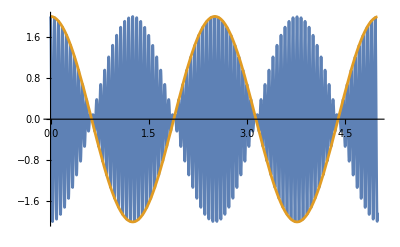

```mathematica
Subscript[ω, 1]=100;
Subscript[ω, 2] = 105;
Plot[{Cos[Subscript[ω, 1] t]+Cos[Subscript[ω, 2] t],2 Cos[(Subscript[ω, 1]-Subscript[ω, 2]) t/2]},{t,0,5}]
```

Taking two random shms which are perpendicular

Cos[5.2782+6.21544 t]

Cos[4.26421+4.45865 t]

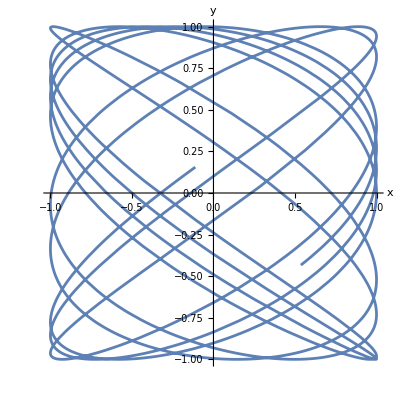

```mathematica
Subscript[A, 1]=1;
Subscript[A, 2] = 1;
(*Disclaimer: each time you run this, a different plot will be obtained*)
Ω1=(1+RandomReal[])*Pi;
Ω2=(1+RandomReal[])*Pi;
del1 = (1+RandomReal[])* Pi;
del2 = (1+RandomReal[]) *Pi;

x[t_]= Subscript[A, 1] Cos[Ω1 t+del1]
y[t_]= Subscript[A, 2] Cos[Ω2 t+del2]
ParametricPlot[{x[t],y[t]},{t,0,10},AxesLabel->{"x", "y"}]
(*As the range of 't' increases the waves cover the entire region*)
```

Ergodicity: all the phase points are equally probable, thus whole phase is covered.

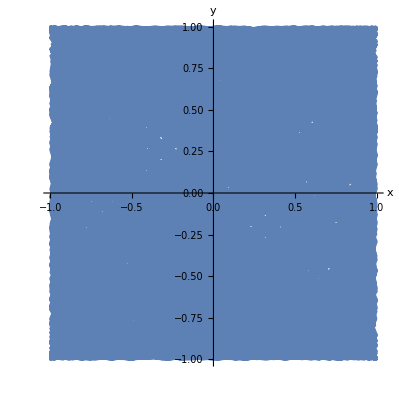

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,250},AxesLabel->{"x", "y"}]
```

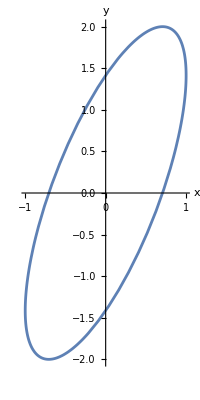

```mathematica
Subscript[A, 1]=1;
Subscript[A, 2] = 2;
Subscript[ω, 1] = Pi;
Subscript[ω, 2] = Pi;
Subscript[δ, 1] =0;
Subscript[δ, 2] =Pi/4;
x[t_]= Subscript[A, 1] Cos[Subscript[ω, 1] t+Subscript[δ, 1]];
y[t_]= Subscript[A, 2] Cos[Subscript[ω, 2] t+Subscript[δ, 2]];

ParametricPlot[{x[t],y[t]},{t,0,2},AxesLabel->{"x","y"}]
```

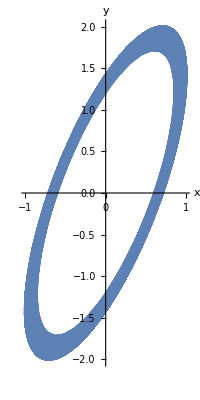

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,1000},AxesLabel->{"x","y"}](*This is thicker because of the bias*)
```

Why’s amplitude decaying with time even when that of the components is fixed? Why does the amplitude “decrease”?
Because of the error.

## [12-02-2025]

Solving the ODEs

Euler’s method

For loop in mathematica

```mathematica
N[Zeta[2],10]
Zeta[2.0]//Timing(*Inbuilt in mathematica, they're much faster*)
```

1.644934067

{0.,1.64493}

```mathematica
Total[Table[1/k^2,{k,1,119999}]]//N//Timing(*Takes more time for same result*)
```

{0.3125,1.64493}

```mathematica
(*For loop*)
sum = 0;
For [k = 1,(*Initialisation*)
	k<= 119999, (*Condition*)
	k++, (*Increment*)
	sum = sum + 1/k^2 (*body*)
]
sum//N//Timing
(*Does the same thing as table, but for loop is slower in general. Yes, in rest of the laptops,it was.*)
```

{0.,1.64493}

```mathematica
For[n=1;x[0]=1,(*Semi-colons separate the two in the same part of for loop*)
n<=100,
n++,
x[n]=-0.5*x[n-1]+Log[Abs[x[n-1]]]]
```

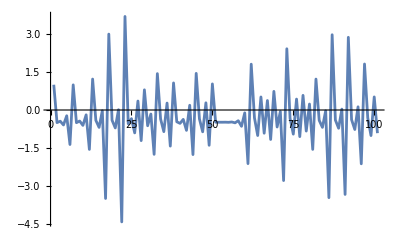

```mathematica
ListPlot[Table[x[n],{n,0,100}],Joined->True]
```

Euler’s method
To solve initial value problems numerically. 
Say the DE is given by-
ẋ =  f(x,t)

To solve it, we discretize the time such that the step size is -
h =t_n-t_(n-1)=(t_f -t_0)/N
then-
x_0=initial value
x_(n+1)=x_n+hf(x_n,t_n)

```mathematica
f[t_,x_]=-2 x;
xi=1;
ti=0;
tf=10;
nmax=100;
h=((tf-ti)/nmax)//N;(*Step size, the less the better*)
datalist={};
xprev = xi;
tprev = ti;
datalist = Append[datalist,{tprev,xprev}];
For[n=1,
n<=nmax,
n++,
tnext=tprev+h;
xnext=xprev+h f[tprev,xprev];
datalist=Append[datalist,{tnext,xnext}];
xprev=xnext;
     tprev=tnext;
]
```

```mathematica
dataplot=ListPlot[datalist,PlotStyle->Red];
solutionplot = Plot[Exp[-2 t],{t,ti,tf}];
```

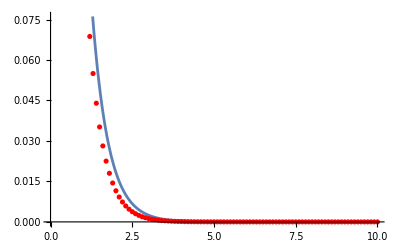

```mathematica
Show[solutionplot,dataplot]
```

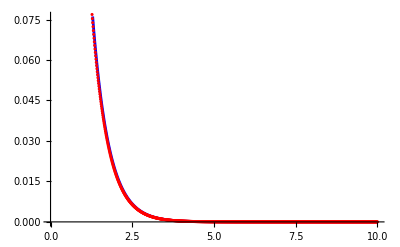

```mathematica
f[t_,x_]=-2 x;
xi1=1;
ti1=0;
tf1=10;
nmax1=1000;(*Increased nmax => more precision*)
h1=((tf1-ti1)/nmax1)//N;(*Smaller the stepsize, less will be the error*)
datalist1={};
xprev1= xi1;
tprev1= ti1;
datalist1 = Append[datalist1,{tprev1,xprev1}];
For[n=1,
n<=nmax1,
n++,
tnext1=tprev1+h1;
xnext1=xprev1+h1 f[tprev1,xprev1];
datalist1=Append[datalist1,{tnext1,xnext1}];
xprev1=xnext1;
     tprev1=tnext1;
]
solutionplot1 = Plot[Exp[-2 t],{t,ti1,tf1},PlotStyle->Blue];
dataplot1 = ListPlot[datalist1,PlotStyle->Red];
Show[solutionplot1,dataplot1]
```

Modified Euler’s

Where we don’t neglect Taylor’s terms upto 2nd power. Given that in the following example, 
At x=0, y=1 with the step size of 0.5 .

```mathematica
f2[x_,y_]= -2 x^3+12 x^2-20 x +8.5
x[0]= 0;
xf = 4;
y[0]=1;
nmax=100;
h=((tf-ti)/nmax)//N;(*Step size, the less the better*)
datalist={};
xprev = xi;
tprev = ti;
datalist = Append[datalist,{tprev,xprev}];
For[n=1,
n<=nmax,
n++,
tnext=tprev+h;
xnext=xprev+h f[tprev,xprev];
datalist=Append[datalist,{tnext,xnext}];
xprev=xnext;
     tprev=tnext;
]
```

```mathematica
H =(xf-x[0])/nmax(*Step size*)



(*At any time t, x[t]=x. Then:*)
y[x]= y[x-1]+f2[x[t-1],y[x-1]]+D[f2,x]./
```

1/25

## Predictor-corrector approach

```mathematica
(*Define function*)f[t_,x_]:=-2 x;

(*Initial conditions*)
xi=1;
ti=0;
tf=10;
nmax=100;
h=N[(tf-ti)/nmax]; (*Step size*)

(*Initialize storage*)
datalist={};
xprev=xi;
tprev=ti;
datalist=Append[datalist,{tprev,xprev}];

(*Modified Euler's Method*)
For[n=1,n<=nmax,n++,(*Predictor step*)xpredictor=xprev+h f[tprev,xprev];
(*Corrector step using an average slope*)tnext=tprev+h;
xnext=xprev+(h/2) (f[tprev,xprev]+f[tnext,xpredictor]);
(*Store result*)datalist=Append[datalist,{tnext,xnext}];
(*Update variables*)xprev=xnext;
tprev=tnext;]

(*Output result*)
datalist;
```